```mathematica
θ[r_,z_]=a+ar*r+az*z+arz*r*z
dθdr[r_,z_]=D[θ[r,z],{r,1}]
dθdz[r_,z_]=D[θ[r,z],{z,1}]
```

a+ar r+az z+arz r z

ar+arz z

az+arz r

```mathematica
ReplCoeff=Simplify[Solve[{θ[r0,z0]==Θ00,θ[r0+dr0,z0]==Θ10,θ[r0,z0+dz0]==Θ01,θ[r0+dr0,z0+dz0]==Θ11},{a,ar,az,arz}][[1]]]
```

{a→(dr0 (dz0 Θ00+z0 (Θ00-Θ01))+r0 (dz0 (Θ00-Θ10)+z0 (Θ00-Θ01-Θ10+Θ11)))/(dr0 dz0),ar→(dz0 (-Θ00+Θ10)+z0 (-Θ00+Θ01+Θ10-Θ11))/(dr0 dz0),az→(dr0 (-Θ00+Θ01)+r0 (-Θ00+Θ01+Θ10-Θ11))/(dr0 dz0),arz→(Θ00-Θ01-Θ10+Θ11)/(dr0 dz0)}

```mathematica
I1=Simplify[ReplaceAll[Integrate[Integrate[(dθdr[r,z]^2+dθdz[r,z]^2)*r,{r,r0,r0+dr0}],{z,z0,z0+dz0}],ReplCoeff]]
```

1/(12 dr0 dz0)(4 dr0^2 r0 (Θ00^2+Θ01^2+(Θ10-Θ11)^2+Θ00 (-2 Θ01+Θ10-Θ11)+Θ01 (-Θ10+Θ11))+dr0^3 (Θ00^2+Θ01^2-2 Θ01 (Θ10-Θ11)+3 (Θ10-Θ11)^2-2 Θ00 (Θ01-Θ10+Θ11))+2 dr0 dz0^2 (Θ00^2+Θ01^2+Θ10^2+Θ00 (Θ01-2 Θ10-Θ11)+Θ10 Θ11+Θ11^2-Θ01 (Θ10+2 Θ11))+4 dz0^2 r0 (Θ00^2+Θ01^2+Θ10^2+Θ00 (Θ01-2 Θ10-Θ11)+Θ10 Θ11+Θ11^2-Θ01 (Θ10+2 Θ11)))

```mathematica
I2=Simplify[ReplaceAll[Integrate[r*θ[r,z0]^2,{r,r0,r0+dr0}],ReplCoeff]]
```

1/12 dr0 (4 r0 (Θ00^2+Θ00 Θ10+Θ10^2)+dr0 (Θ00^2+2 Θ00 Θ10+3 Θ10^2))

```mathematica
I3=Simplify[ReplaceAll[Integrate[r*θ[r,z0+dz0]^2,{r,r0,r0+dr0}],ReplCoeff]]
```

1/12 dr0 (4 r0 (Θ01^2+Θ01 Θ11+Θ11^2)+dr0 (Θ01^2+2 Θ01 Θ11+3 Θ11^2))

```mathematica
I4= Simplify[ReplaceAll[Integrate[θ[r0+dr0,z]^2,{z,z0,z0+dz0}],ReplCoeff]]
```

1/3 dz0 (Θ10^2+Θ10 Θ11+Θ11^2)

```mathematica
I5= Simplify[ReplaceAll[Integrate[r*θ[r,z0],{r,r0,r0+dr0}],ReplCoeff]]
```

1/6 dr0 (3 r0 (Θ00+Θ10)+dr0 (Θ00+2 Θ10))

```mathematica
ReplShift[di_,dj_]:=Module[{i0,i1,j0,j1},
i0=di+1;i1=i0+1;j0=dj+1;j1=j0+1;
{Θ01->mΘ[[i0,j1]],Θ00->mΘ[[i0,j0]],Θ11->mΘ[[i1,j1]],Θ10->mΘ[[i1,j0]],z0->mz0[[dj+1]],r0->mr0[[di+1]],dz0->dH,dr0->mr0[[di+2]]-mr0[[di+1]]}
]
```

```mathematica
MainFunc[m0_,m1_,n0_]:=Module[{i,j,k},
dH=H/n0;
dR0=R0/m0;
dR1=(R1-R0)/m1;
mΘ=Array[Θ,{m0+m1+1,n0+1}];
mVΘ={};
For[i=1,i≤m0+m1+1,i++,
For[j=1,j≤n0+1,j++,
AppendTo[mVΘ,mΘ[[i,j]]];
];
];
mz0=Table[0,{i,0,n0}];
For[i=0,i≤n0,i++,
mz0[[i+1]]=i*dH;
];
dR0=R0/m0;dR1=(R1-R0)/m1;
mr0=Table[0,{i,0,m0+m1}];
For[i=0,i≤m0,i++,
mr0[[i+1]]=i*dR0;
];
For[i=1,i≤m1,i++,
mr0[[i+m0+1]]=R0+i*dR1;
];
Φ=0;
For[i=0,i<m0+m1,i++,
For[j=0,j<n0,j++,
Φ+=ReplaceAll[I1,ReplShift[i,j]];
];
];
j=0;
For[i=m0,i<m0+m1,i++,
Φ+=α/λ*ReplaceAll[I2,ReplShift[i,j]];
];
j=n0-1;
For[i=0,i<m0+m1,i++,
Φ+=α/λ*ReplaceAll[I3,ReplShift[i,j]];
];
i=m0+m1-1;
For[j=0,j<n0,j++,
Φ+=R1*α/λ*ReplaceAll[I4,ReplShift[i,j]];
];
j=0;
For[i=0,i<m0,i++,
Φ-=2*q/λ*ReplaceAll[I5,ReplShift[i,j]];
];
mE={};
nVΘ=Length[mVΘ];
For[i=1,i≤nVΘ,i++,
AppendTo[mE,D[Φ,{mVΘ[[i]],1}]==0];
];
ReplΘ=Solve[mE,mVΘ][[1]];
ΘMin=ReplaceAll[mVΘ[[1]],ReplΘ];
ΘMax=ΘMin;
For[i=1,i≤nVΘ,i++,
ΘCurr=ReplaceAll[mVΘ[[i]],ReplΘ];
If[ΘMax<ΘCurr,ΘMax=ΘCurr];
If[ΘMin>ΘCurr,ΘMin=ΘCurr];
];
s=0;
j=0;
For[i=0,i<m0,i++,
s+=ReplaceAll[I5,ReplShift[i,j]];
];
ΘAvg=s/(R0^2/2);
RH=ReplaceAll[ΘAvg/(π*R0^2),ReplΘ];
Print["R1=",R1,"  RH=",RH];
]
```

```mathematica
MainCircle[m0_,m1_,n0_]:=Module[{},
q=1;
α=10;
λ=236;
R0 = 0.01;
VN=0.00002;
bWas=False;
mG={};
For[R1=0.05,R1≤0.14,R1+=0.002,
H=VN/(π*R1^2);
MainFunc[m0,m1,n0];
If[bWas,
If[RHMin>RH,
R1Min=R1;RHMin=RH;
];
,
R1Min=R1;RHMin=RH;
bWas=True;
];
AppendTo[mG,{R1,RH}];
];
HMin=VN/(π*R1Min^2);
Print["R1Min=",R1Min,"  HMin=",HMin,"  RHMin=",RHMin];
ListPlot[mG,PlotJoined->True];
]
```

```mathematica
MainCircle[5,2,8]
mG050208=mG;
Put[mG050208,"G050208.txt"];
```

R1=0.05  RH=6.45907

R1=0.052  RH=6.04411

R1=0.054  RH=5.67506

R1=0.056  RH=5.34647

R1=0.058  RH=5.05366

R1=0.06  RH=4.79258

R1=0.062  RH=4.55973

R1=0.064  RH=4.35207

R1=0.066  RH=4.16697

R1=0.068  RH=4.00212

R1=0.07  RH=3.85551

R1=0.072  RH=3.72539

R1=0.074  RH=3.61021

R1=0.076  RH=3.50858

R1=0.078  RH=3.41931

R1=0.08  RH=3.34131

R1=0.082  RH=3.27363

R1=0.084  RH=3.2154

R1=0.086  RH=3.16586

R1=0.088  RH=3.1243

R1=0.09  RH=3.0901

R1=0.092  RH=3.06269

R1=0.094  RH=3.04154

R1=0.096  RH=3.02619

R1=0.098  RH=3.01619

R1=0.1  RH=3.01114

R1=0.102  RH=3.01066

R1=0.104  RH=3.01443

R1=0.106  RH=3.02211

R1=0.108  RH=3.0334

R1=0.11  RH=3.04802

R1=0.112  RH=3.06572

R1=0.114  RH=3.08623

R1=0.116  RH=3.10934

R1=0.118  RH=3.13482

R1=0.12  RH=3.16246

R1=0.122  RH=3.19205

R1=0.124  RH=3.22343

R1=0.126  RH=3.2564

R1=0.128  RH=3.29079

R1=0.13  RH=3.32645

R1=0.132  RH=3.36322

R1=0.134  RH=3.40096

R1=0.136  RH=3.43952

R1=0.138  RH=3.47878

R1=0.14  RH=3.51862

R1Min=0.102  HMin=0.000611899  RHMin=3.01066

```mathematica
MainCircle[10,4,16]
mG100416=mG;
Put[mG100416,"G100416.txt"];
```

R1=0.05  RH=6.4892

R1=0.052  RH=6.07858

R1=0.054  RH=5.71425

R1=0.056  RH=5.39078

R1=0.058  RH=5.10349

R1=0.06  RH=4.84834

R1=0.062  RH=4.62183

R1=0.064  RH=4.42094

R1=0.066  RH=4.24305

R1=0.068  RH=4.08585

R1=0.07  RH=3.94734

R1=0.072  RH=3.82577

R1=0.074  RH=3.7196

R1=0.076  RH=3.62745

R1=0.078  RH=3.54813

R1=0.08  RH=3.48056

R1=0.082  RH=3.42379

R1=0.084  RH=3.37696

R1=0.086  RH=3.33931

R1=0.088  RH=3.31014

R1=0.09  RH=3.28883

R1=0.092  RH=3.2748

R1=0.094  RH=3.26755

R1=0.096  RH=3.2666

R1=0.098  RH=3.27152

R1=0.1  RH=3.2819

R1=0.102  RH=3.29739

R1=0.104  RH=3.31763

R1=0.106  RH=3.34231

R1=0.108  RH=3.37113

R1=0.11  RH=3.40381

R1=0.112  RH=3.4401

R1=0.114  RH=3.47974

R1=0.116  RH=3.52252

R1=0.118  RH=3.5682

R1=0.12  RH=3.61658

R1=0.122  RH=3.66746

R1=0.124  RH=3.72067

R1=0.126  RH=3.77602

R1=0.128  RH=3.83334

R1=0.13  RH=3.89247

R1=0.132  RH=3.95327

R1=0.134  RH=4.01558

R1=0.136  RH=4.07926

R1=0.138  RH=4.1442

R1=0.14  RH=4.21025

R1Min=0.096  HMin=0.000690777  RHMin=3.2666

```mathematica
MainCircle[15,6,24]
mG150624=mG;
Put[mG150624,"G150624.txt"];
```

R1=0.05  RH=6.49618

R1=0.052  RH=6.08665

R1=0.054  RH=5.72352

R1=0.056  RH=5.40138

R1=0.058  RH=5.11554

R1=0.06  RH=4.86198

R1=0.062  RH=4.6372

R1=0.064  RH=4.43818

R1=0.066  RH=4.2623

R1=0.068  RH=4.10727

R1=0.07  RH=3.97109

R1=0.072  RH=3.85202

R1=0.074  RH=3.7485

R1=0.076  RH=3.65919

R1=0.078  RH=3.58288

R1=0.08  RH=3.5185

R1=0.082  RH=3.46511

R1=0.084  RH=3.42185

R1=0.086  RH=3.38796

R1=0.088  RH=3.36275

R1=0.09  RH=3.3456

R1=0.092  RH=3.33596

R1=0.094  RH=3.3333

R1=0.096  RH=3.33716

R1=0.098  RH=3.34711

R1=0.1  RH=3.36276

R1=0.102  RH=3.38373

R1=0.104  RH=3.4097

R1=0.106  RH=3.44034

R1=0.108  RH=3.47537

R1=0.11  RH=3.51451

R1=0.112  RH=3.55751

R1=0.114  RH=3.60412

R1=0.116  RH=3.65412

R1=0.118  RH=3.7073

R1=0.12  RH=3.76344

R1=0.122  RH=3.82236

R1=0.124  RH=3.88388

R1=0.126  RH=3.94782

R1=0.128  RH=4.01401

R1=0.13  RH=4.08231

R1=0.132  RH=4.15257

R1=0.134  RH=4.22463

R1=0.136  RH=4.29837

R1=0.138  RH=4.37366

R1=0.14  RH=4.45037

R1Min=0.094  HMin=0.000720484  RHMin=3.3333

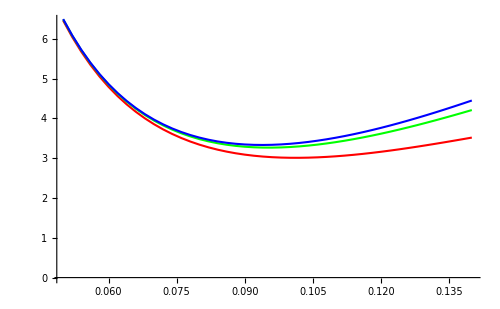

```mathematica
G050208=ListPlot[mG050208,PlotJoined->True,PlotStyle->{RGBColor[1,0,0],Thickness[0.003]},ImageSize->100];
G100416=ListPlot[mG100416,PlotJoined->True,PlotStyle->{RGBColor[0,1,0],Thickness[0.003]},ImageSize->100];
G150624=ListPlot[mG150624,PlotJoined->True,PlotStyle->{RGBColor[0,0,1],Thickness[0.003]},ImageSize->100];
Show[G050208,G100416,G150624,ImageSize->500]
```